```mathematica
A[]:=1/2((xD-xA)+(xC-xB))(pH-pL);
VA1[]:=pH/(pL-pH)Pi(1/2 d)^2(xB-xA);
VA2[]:=tL/(tH-tL)Pi(1/2 d)^2(xD-xA);
WorkTotal[]:=Pi(1/2 d)^2 A[];
QIn[]:=(pL*vA)/tL(7/2(tH-tL)+tH*Log[pH/pL]);
Efficiency[]:=WorkTotal[]/QIn[];
MaxEfficiency[]:=1-tL/tH;
```

```mathematica
d=32.5*10^-3;
m=48.5*10^-3;
pAtm=101.3*10^3;
```

```mathematica
{xA,xB,xC,xD}={0,-5.5500,14.4375,18.6750}*10^-3;
{pL,pH}={99.64,102.20}*10^3;
{tL,tH}={280.25,327.76};
ScientificForm[A[]]
ScientificForm[VA1[]]
ScientificForm[VA2[]]
vA=Mean[{VA1[],VA2[]}];
ScientificForm[vA]
ScientificForm[WorkTotal[]]
ScientificForm[QIn[]]
ScientificForm[Efficiency[]]
ScientificForm[MaxEfficiency[]]
```

4.9488×10^1

1.83806×10^-4

9.13856×10^-5

1.37596×10^-4

4.10541×10^-2

8.54156

4.80639×10^-3

1.44954×10^-1

```mathematica
{xA,xB,xC,xD}={0,-6.1125,13.4250,17.7375}*10^-3;
{pL,pH}={99.62,102.14}*10^3;
{tL,tH}={280.48,328.19};
ScientificForm[A[]]
ScientificForm[VA1[]]
ScientificForm[VA2[]]
vA=Mean[{VA1[],VA2[]}];
ScientificForm[vA]
ScientificForm[WorkTotal[]]
ScientificForm[QIn[]]
ScientificForm[Efficiency[]]
ScientificForm[MaxEfficiency[]]
```

4.69665×10^1

2.05528×10^-4

8.65051×10^-5

1.46016×10^-4

3.89623×10^-2

9.08532

4.28849×10^-3

1.45373×10^-1

{0.0176667,0.0226667,0.0263333,0.0283333,0.0323333,0.034}

{0.000312111,0.000513778,0.000693444,0.000802778,0.00104544,0.001156}

-0.0091695+58.586 x

58.586

1.33484

0.995777

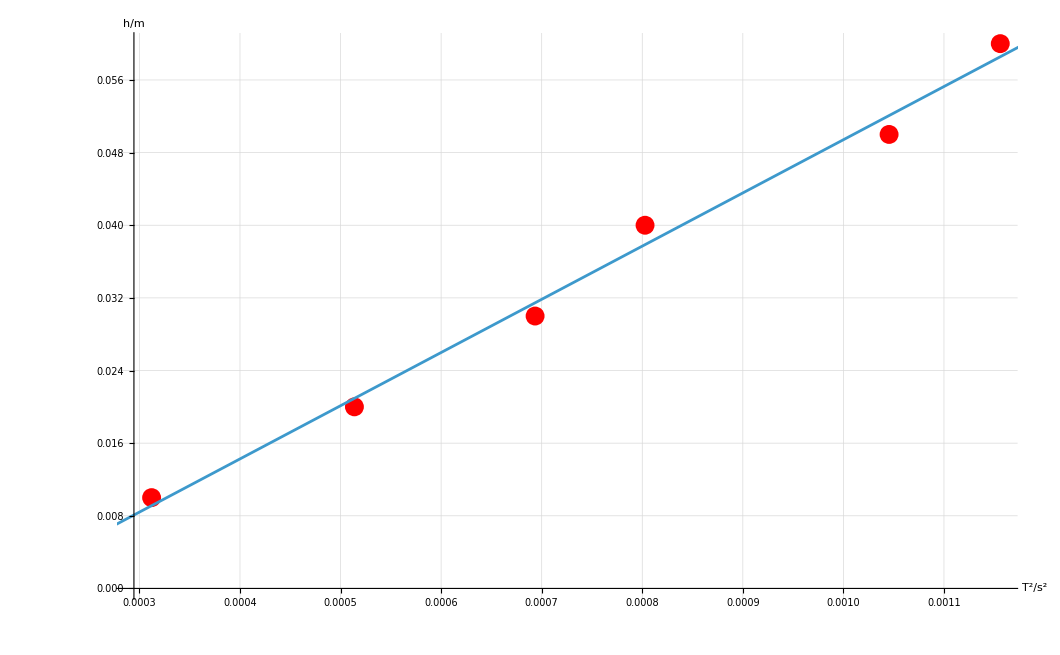

```mathematica
h=Array[10#&,6]*10^-3;
t={{17,19,17},{23,22,23},{27,26,26},{29,28,28},{32,32,33},{34,35,33}}*10^-3;
tMeans=Map[Mean,t];
tMeanSquares=Map[#^2&,tMeans];
N[tMeans]
N[tMeanSquares]
data=Array[{tMeanSquares[[#]],h[[#]]}&,6];
fit=Fit[data,{1,x},x]
k=Coefficient[fit,x]
gamma=4 Pi^2 m/(Pi*(1/2 d)^2*pAtm)k
corr=Correlation[tMeanSquares,h];
N[corr]
Show[Show[ListPlot[data,PlotStyle->Red],Plot[fit,{x,(15*10^-3)^2,(40*10^-3)^2}]],GridLines->Automatic,AxesLabel->{"T^2/s^2","h/m"},LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0],Italic}]
```